# Generating Mario Levels

Samion Suwito

Abstract
I wanted to generate Mario Levels so I generated Mario Levels (W.I.P.)

## Introduction

I wanted to generate Mario Levels so I generated Mario Levels

## Processing Images of Mario Levels

I have collected images of levels from Super Mario Bros. and Super Mario Bros. The Lost Levels. They are all Overworld Levels as their level designs don't differ too much and will have a clearer pattern. I then divide the image into a grid of 16x16px and process each square to map the level into an array.

### Loading the images

I load the images of the levels and crop any extra stuff whilst removing the alpha channel just to simplify it.

```mathematica
map11 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/7c0ee3b5-1a3d-4bd8-a092-7f1f54e4e20d"](https://www.wolframcloud.com/obj/7c0ee3b5-1a3d-4bd8-a092-7f1f54e4e20d)],{{0,0},{-240,0}}]];
map21 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/ac4c0aef-6687-4f31-a240-462039f34d96"](https://www.wolframcloud.com/obj/ac4c0aef-6687-4f31-a240-462039f34d96)],{{0,0},{-240,-240}}]];
map31 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/9bc488a8-13ba-48e6-a60d-3f03f80c9e8b"](https://www.wolframcloud.com/obj/9bc488a8-13ba-48e6-a60d-3f03f80c9e8b)],{{0,0},{-240,-240}}]];
map41 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/6bfbbb3f-cd90-4df1-adc4-4646cc14fb22"](https://www.wolframcloud.com/obj/6bfbbb3f-cd90-4df1-adc4-4646cc14fb22)],{{0,0},{-240,0}}]];
map51 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/17d83563-90ef-4dc9-b97e-51883ffdaccc"](https://www.wolframcloud.com/obj/17d83563-90ef-4dc9-b97e-51883ffdaccc)],{{0,0},{-240,0}}]];
map52 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/916d095e-05ba-4759-a8ae-491755b9f94a"](https://www.wolframcloud.com/obj/916d095e-05ba-4759-a8ae-491755b9f94a)],{{0,0},{-240,-240}}]];
map61 = RemoveAlphaChannel[CloudImport[["https://www.wolframcloud.com/obj/2a8960ac-f087-4151-a73d-28f17ad0f96f"](https://www.wolframcloud.com/obj/2a8960ac-f087-4151-a73d-28f17ad0f96f)]];
map71 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/bb972b44-0a50-480b-90a5-042e4487d72f"](https://www.wolframcloud.com/obj/bb972b44-0a50-480b-90a5-042e4487d72f)],{{0,0},{-240,0}}]];
map81 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/02a7838b-6ac5-4491-a550-6414c3fdd40c"](https://www.wolframcloud.com/obj/02a7838b-6ac5-4491-a550-6414c3fdd40c)],{{0,0},{-240,0}}]];
mapl11 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/65664715-e560-432d-918c-b7be4509ecb0"](https://www.wolframcloud.com/obj/65664715-e560-432d-918c-b7be4509ecb0)],{{0,0},{-240,0}}]];
mapl31 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/9efa1c36-2e01-42f1-8537-ba46c5f4f81a"](https://www.wolframcloud.com/obj/9efa1c36-2e01-42f1-8537-ba46c5f4f81a)],{{0,0},{-240,-240}}]];
mapl41 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/a0861449-e825-42bd-a06d-e56cdced80a8"](https://www.wolframcloud.com/obj/a0861449-e825-42bd-a06d-e56cdced80a8)],{{0,0},{-240,-240}}]];
mapl42 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/d4791678-fb0f-493b-8644-65a3daa12c09"](https://www.wolframcloud.com/obj/d4791678-fb0f-493b-8644-65a3daa12c09)],{{0,0},{-240,0}}]];
mapl61 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/353633ec-e377-4e69-9e62-c6706633d7cd"](https://www.wolframcloud.com/obj/353633ec-e377-4e69-9e62-c6706633d7cd)],{{0,0},{-240,0}}]];
mapl71 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/1993bd2f-d0b9-44ec-83ec-9e538491dc2a"](https://www.wolframcloud.com/obj/1993bd2f-d0b9-44ec-83ec-9e538491dc2a)],{{0,0},{-240,0}}]];
```

### Creating a function to process each block

I get the sprite of each type of block by partitioning the image and taking the position of the block

```mathematica
ground = ImageData[ImagePartition[map11,16][[-1]][[1]]]|ImageData[ImagePartition[mapl11,16][[-1]][[1]]];
passthrough = ImageData[ImagePartition[map31,16][[-6]][[85]]];
hard =  ImageData[ImagePartition[map11,16][[-3]][[199]]];
lucky =  ImageData[ImagePartition[map11,16][[-6]][[17]]]|ImageData[ImagePartition[map31,16][[-6]][[17]]];
brick =  ImageData[ImagePartition[map11,16][[-6]][[21]]]|ImageData[ImagePartition[mapl11,16][[6]][[20]]];
tpipe =  ImageData[ImagePartition[map11,16][[-6]][[47]]] | ImageData[ImagePartition[map11,16][[-6]][[48]]] | ImageData[ImagePartition[map51,16]⟦-5⟧[[46]]] | ImageData[ImagePartition[map51,16]⟦-5⟧[[45]]]|ImageData[ImagePartition[map31,16][[-4]][[69]]] |ImageData[ImagePartition[map31,16][[-4]][[68]]];
pipe =  ImageData[ImagePartition[map11,16][[-5]][[47]]] | ImageData[ImagePartition[map11,16][[-5]][[48]]] | ImageData[ImagePartition[map51,16]⟦-4⟧[[46]]] | ImageData[ImagePartition[map51,16]⟦-4⟧[[45]]]|ImageData[ImagePartition[map31,16][[-3]][[69]]]|ImageData[ImagePartition[map31,16][[-3]][[68]]];
bullet = ImageData[ImagePartition[map71,16][[-3]][[20]]]|ImageData[ImagePartition[map71,16][[-3]][[29]]]|ImageData[ImagePartition[map71,16][[-3]][[47]]];
```

I then use these values to create a function to transfer each block in the image to a number.

```mathematica
ConvertBlocks[image_]:=Switch[ImageData[image],
ground,1,
hard,1,
lucky,1,
brick,1,
pipe|tpipe,1,
bullet,1,
passthrough,1,
Except["else"],0]
```

I can now convert all of these images into arrays and check the function working through creating an Array Plot

```mathematica
array11=Map[ConvertBlocks,ImagePartition[map11,16],{2}];
array21=Map[ConvertBlocks,ImagePartition[map21,16],{2}];
array31=Map[ConvertBlocks,ImagePartition[map31,16],{2}] ;
array41=Map[ConvertBlocks,ImagePartition[map41,16],{2}];
array51=Map[ConvertBlocks,ImagePartition[map51,16],{2}];
array61=Map[ConvertBlocks,ImagePartition[map61,16],{2}];
array71=Map[ConvertBlocks,ImagePartition[map71,16],{2}];
array81=Map[ConvertBlocks,ImagePartition[map81,16],{2}];
arrayl11 = Map[ConvertBlocks, ImagePartition[mapl11,16],{2}];
arrayl31 = Map[ConvertBlocks, ImagePartition[mapl31,16],{2}];
arrayl41 = Map[ConvertBlocks, ImagePartition[mapl41,16],{2}];
arrayl42 = Map[ConvertBlocks, ImagePartition[mapl42,16],{2}];
arrayl61 = Map[ConvertBlocks, ImagePartition[mapl61,16],{2}];
arrayl71 = Map[ConvertBlocks, ImagePartition[mapl71,16],{2}];
ArrayPlot/@{array11,array21,array31,array41,array51,array61,array71,array81,arrayl11,arrayl31,arrayl41,arrayl42,arrayl61,arrayl71}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Simplifying and Gathering the images

I then create every a 240x240px possible square of each level that doesn't intersect the grid boxes of the level and convert each of those squares into a 15x15 array.

```mathematica
maps = {map11, map21, map31, map41, map51, map52, map61, map71, map81, mapl11, mapl31, mapl41, mapl42, mapl61, mapl71};
imagedataset = Flatten[
      Table[
        Table[ImageTake[map, 240, {i, i + 240 - 1}],
          {i, 1, ImageDimensions[map][[1]] - 240 + 16, 16} (* thx isabel*)
          ], {map, maps}
        ]
      ];
dataset = Map[ConvertBlocks, ImagePartition[#, 16], {2}] & /@ imagedataset;
```

This gives us 3747 squares as shown from the output below

```mathematica
Dimensions[dataset]
```

{3747,15,15}

## Attempting to generate using a single Wolfram Function

I first attempted trying to generate levels using SequencePredict and LearnDistribution to create Mario Levels which gave an ok output but now a very good one.

### Using Sequence Predict

I trained SequencePredict on each row of a square to see what it would generate

```mathematica
sp1 = SequencePredict[Table[entry[[1]],{entry,dataset}]];
sp2 = SequencePredict[Table[entry[[2]],{entry,dataset}]];
sp3 = SequencePredict[Table[entry[[3]],{entry,dataset}]];
sp4 = SequencePredict[Table[entry[[4]],{entry,dataset}]];
sp5 = SequencePredict[Table[entry[[5]],{entry,dataset}]];
sp6 = SequencePredict[Table[entry[[6]],{entry,dataset}]];
sp7 = SequencePredict[Table[entry[[7]],{entry,dataset}]];
sp8 = SequencePredict[Table[entry[[8]],{entry,dataset}]];
sp9 = SequencePredict[Table[entry[[9]],{entry,dataset}]];
sp10 = SequencePredict[Table[entry[[10]],{entry,dataset}]];
sp11= SequencePredict[Table[entry[[11]],{entry,dataset}]];
sp12 = SequencePredict[Table[entry[[12]],{entry,dataset}]];
sp13 = SequencePredict[Table[entry[[13]],{entry,dataset}]];
sp14 = SequencePredict[Table[entry[[14]],{entry,dataset}]];
sp15 = SequencePredict[Table[entry[[15]],{entry,dataset}]];
```

I then created an ArrayPlot to visualize how this would look like

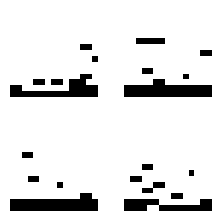

```mathematica
GraphicsGrid[
Table[
Table[
ArrayPlot[{sp1[{0},"RandomNextElement"->15],
sp2[{0},"RandomNextElement"->15],
sp3[{0},"RandomNextElement"->15],
sp4[{0},"RandomNextElement"->15],
sp5[{0},"RandomNextElement"->15],
sp6[{0},"RandomNextElement"->15],
sp7[{0},"RandomNextElement"->15],
sp8[{0},"RandomNextElement"->15],
sp9[{0},"RandomNextElement"->15],
sp10[{0},"RandomNextElement"->15],
sp11[{0},"RandomNextElement"->15],
sp12[{0},"RandomNextElement"->15],
sp13[{0},"RandomNextElement"->15],
sp14[{1},"RandomNextElement"->15],
sp15[{1},"RandomNextElement"->15]}]
,2]
,2]
]
```

### Using Learn Distribution

I then attempted to use Learn Distribution to see what it would produce. I need to change the dataset a bit because Wolfram Language assumes that if there's only 0s then it's a NumericalVector instead of a BooleanVector meaning I'll have decimals so I'll simply change one value to a 1 in the first two rows.

```mathematica
lddataset = dataset;
lddataset[[1]][[1]][[1]] = 1;
lddataset[[1]][[2]][[1]] = 1;
ld = LearnDistribution[lddataset];
```

I then visualized it the same way I did for SequencePredict

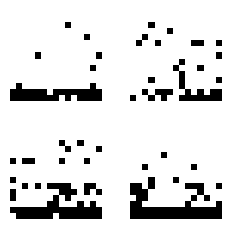

```mathematica
GraphicsGrid[
Table[
Table[
ArrayPlot[RandomVariate[ld]]
,2]
,2]
]
```

Overall the results from SequencePredict look better but LearnDistribution did train faster.

## Attempting to Generate using Learn Distribution

I actually first attempted to generate levels using a GAN but it took too long and the results that came out weren't so good. But the discriminator was working quite well so I decided to replace the generator with LearnDistribution since it trains faster than SequencePredict so I can get results faster. The way I've structured it is that the Discriminator will first be trained on the original Mario Levels and random bad arrays and then LearnDistribution will create their predicted arrays based off learning from the Mario Levels and if the Discriminator thinks what LearnDistribution made was good then it would put it in the arrays for LearnDistribution to learn off from. Whether or not the LearnDistribution's sample was good or not, the discriminator will put it in it's dataset to learn off from as bad.

### The Discriminator

The discriminator is a neural network that determines how close is it to a Mario Level with 1 being a Mario Level.

```mathematica
convolutionBlock[args___]:=NetChain[{ConvolutionLayer[args],NormalizationLayer[],ElementwiseLayer["SELU"],DropoutLayer[0.4]}];
discriminator=NetFlatten@NetChain[{
	convolutionBlock[64,{3,3}],
	convolutionBlock[64,{3,3}],
	LinearLayer[{}],
	LogisticSigmoid
},
	"Input"->{1,15,15}
]
```

NetChain[<>]

We also need to re-format our dataset since the neural network can only take in a 1x15x15 array and not a 15x15.

```mathematica
discriminatorDataset = ArrayReshape[#,{1,15,15}]&/@dataset;
```

We then need to just make a set of bad data as an example

```mathematica
badDataset=Table[{Table[Table[RandomInteger[],15],15]},1000];
```

Now we need to turn these sets into a set of rules for the neural network to train on

```mathematica
datasetRules=Join[Table[entry->1,{entry,discriminatorDataset}],Table[entry->0,{entry,badDataset}]];
```

#### The LearnDistribution

We also need to give data to the LearnDistribution so we will first give it the Mario Levels and build on to it.

```mathematica
lddataset = dataset;
lddataset[[1]][[1]][[1]] = 1;
lddataset[[1]][[2]][[1]] = 1;
```

### Putting it all together

We now need to make a few variables to put these all together

```mathematica
ldlist = {}; (* Every creation from LearnDistribution *)
ldsetrules = {}; (* Making the list of rules to make whatever the LD generates bad *)
datagen = {}; (* combining ldsetrules with datasetRules *)
goodLD = {}; (* Samples from LearnDistribution going back to LearnDistribution *)
```

The variables distrained will now only be used for the trained discriminator and ld will now only be used for the trained LearnDistribution

```mathematica
TrainLDNN[rounds_,increase_]:=Table[
(* Need to put list bracket around entry since NN only accepts 1x15x15 not 15x15*)
ldsetrules=Table[{entry}->0,{entry,ldlist}]; 
datagen = Join[datasetRules,ldsetrules];
(* Training the Discriminator here *)
distrained = NetTrain[discriminator,datagen,ValidationSet->Scaled[0.2]]; 
ld = LearnDistribution[Join[lddataset,goodLD]];
Table[
randomld = {RandomVariate[ld]};
If[distrained[randomld]>0.999,goodLD=Append[goodLD,randomld]];
ldlist=Append[ldlist,randomld];
,increase];
(* just to see the progress *)    
ArrayPlot[goodLD[[-1]]]
,rounds]
```

Need to run this and show an example

## Finding patterns to make the level more realistic

I'm going to apply general patterns of Mario Levels in order to construct the Mario Level to become more realistic

### The First and Second Layers (Very Top Sky)

The first 2 layers are always empty.

```mathematica
layer1 = Table[0,15]
layer2 = Table[0,15]
```

### The Fifteenth and Fourteenth Layers (Ground)

The bottom 2 layers are always identical so whatever the bottom layer is the second bottom layer also is. The following code will generate the bottom layer and the 2nd bottom layer will just be the same

```mathematica
layer15 = sp15[{1}, "RandomNextElement" -> 15];
layer14 = layer15
```

{1,1,1,1,1,1,1,0,0,0,0,0,0,1,1}

### The Thirteenth, Twelfth and Eleventh Layer (1 Block above Ground)

For the thirteenth layer the following rules are often applied

```mathematica
layer13 = sp13[{0},"RandomNextElement"->15]
```

{1,1,1,1,0,1,0,1,1,0,0,0,0,1,1}

If a block is above a gap, remove it.

```mathematica
Table[If[layer15[[i]]===0,layer13[[i]]=0,Nothing],{i,15}];
layer13
```

{1,1,1,1,0,1,0,0,0,0,0,0,0,1,1}

If there are just two consecutive blocks with nothing else to the left or right of them then it has to be a pipe

```mathematica
test = StringJoin@@ToString/@layer13
```

111101000000011

```mathematica
test = "000011000"
```

000011000

```mathematica
First[#]+1&/@StringPosition[test,"0110"]
```

{5}

If there is just one block with nothing else to the left or right of them then it can either be a wall or a bullet bill launcher

If there are more than two consecutive blocks it's most likely a staircase

The twelfth an eleventh layer then follow the thirteenth layer with pipes varying from sizes and staircases continuing their pattern

### Rest of the layers

The rest of the layers either follow a staircase or are bricks and lucky blocks which can be generated from LearnDistribution.

## Turning the array back into an image

I now want to turn the array back into an image so I've created this function which replaces values back to images

```mathematica
ConvertBack[layer_]:=layer/.
{0->ImagePartition[map11,16][[1]][[1]] (*Sky*),
1->ImagePartition[map11,16][[-1]][[1]] (*Ground*),
2->ImagePartition[map11,16][[-3]][[199]] (* Hard Block *),
3->ImagePartition[map11,16][[-6]][[21]](* Brick *),
4->ImagePartition[map11,16][[-5]][[47]] (* Left Pipe *),
5->ImagePartition[map11,16][[-5]][[48]](* Right Pipe *)}
```

Need to join the image then done

## Future Work

Use ROM Hacking to create the level in Super Mario Bros. and use OpenAI Gym Retro to check its playability.